# 1. Preparing files

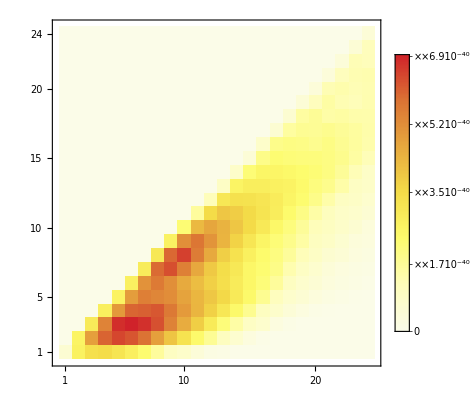

```mathematica
path="/home/michaszko/Documents/Neutrina/Opus/T2K_nu";
type="LFG";
mecDim=24;
eventsNumber=0.5*10^6;
scalingFactor=5*10^38;
crossSection=5.92923*10^-40;

Δcos={0.8,0.4,0.1,0.1,0.05,0.05,0.04,0.04,0.02};
dcos={-1,0.2,0.6,0.7,0.8,0.85,0.9,0.94,0.98,1};

dmom={
{5,30000},
{5,300,400,500,600,800},
{5,300,400,500,600,800,1000},
{5,300,400,500,600,800,1000},
{5,300,400,500,600,800,1000,1250},
{5,300,400,500,600,800,1000,1250,1500},
{5,400,500,600,800,1250,2000,3000},
{5,400,500,600,800,1000,1250,1500,2000,3000,5000},{5,500,700,900,1500,2000,3000,5000,30000}};
Δmom={
{29995},
{295,100,100,100,200},
{295,100,100,100,200,200},
{295,100,100,100,200,200},
{295,100,100,100,200,200,250},
{295,100,100,100,200,200,250,250},
{395,100,100,200,450,750,1000},
{395,100,100,200,200,250,250,500,1000,2000},
{495,200,200,600,500,1000,2000,25000}};

dmom2=Most[dmom[[#]]]+Δmom[[#]]/2&/@Range[Length[dmom]];


binning={1,5,6,6,7,8,7,10,8};
(*Total[Take[binning,#]]&/@Range[Length[binning]]*)
binning2={0,1,6,12,18,25,33,40,50,58};

widthVanilla=Flatten[Δcos*Δmom];

(************************************)

mecVanillaDist=Import[path<>"/data/matrix_"<>type<>".dat"];
nonmecVanilla=Flatten[Import[path<>"/data/cros_total_nuwro_"<>type<>".dat"]];
danielVanilla=Flatten[Import[path<>"/data/cros_total_daniel.dat"]];
covNonVanilla=Import[path<>"/data/daniel_covariance_vanilla.dat"]/scalingFactor^2;

(*********************************************)

mecDist=mecVanillaDist/eventsNumber*crossSection*1000/widthVanilla;

covVanilla=PseudoInverse[covNonVanilla][[Range[58],Range[58]]];
errorVanilla=1/Sqrt[Diagonal[covVanilla[[Range[58],Range[58]]]]];

proper[x_]:=Take[x,{binning2[[#]]+1,binning2[[#+1]]}]&/@Range[Length[binning2]-1];

newVanilla=mecDist.ConstantArray[1,mecDim^2];

(**********************************************)

(*MatrixPlot[Transpose@mecDist];

RectangleChart[
Thread[{Subscript[Δp, T],Take[Plus@@Transpose[mecDist],{#,-1,lenPL}]}],
GridLines->Automatic,
BarSpacing->None,
ImageSize->Large,
PlotLabel->(#-1)]&/@Range[lenPT-1];*)

MatrixPlot[Partition[Plus@@mecDist,mecDim],DataReversed->True,PlotLegends->Automatic,ColorFunction->"TemperatureMap"]
```

# 2. Test χ^2

## χ^2 bez kowariancji

```mathematica
Clear[χ]
χ=((danielVanilla-nonmecVanilla-newVanilla)/errorVanilla)^2;

χ=Total[Most[#]&/@proper[χ],2]
```

69.6126

## χ^2 z kowariancją

```mathematica
a=Flatten[danielVanilla-nonmecVanilla-newVanilla];
a.covVanilla.a
Total[Most[#]&/@proper[a*(covVanilla.a)],2]
#&/@proper[a*(covVanilla.a)]//MatrixForm
```

22359.9

10.7165

({4.37752}
{3.43613,1.75568,-9.08133,-30.6411,969.478}
{29.5619,-0.00913705,-17.7445,2.21949,-13.0422,-201.473}
{-23.0299,5.42222,-1.8353,16.4547,0.243736,6688.17}
{-7.8827,-6.83186,-0.202128,-26.385,0.199352,-0.194126,2923.2}
{-0.970242,0.584925,-0.135929,1.91778,-21.4034,-9.29529,0.0139555,13226.7}
{-3.87924,2.23049,12.8607,43.8611,21.1408,20.6238,-813.716}
{-8.92609,-2.41088,20.2742,2.41671,-8.10224,10.8477,13.3834,13.5463,-10.8656,-442.134}
{5.1356,5.63991,-6.31901,1.06268,1.37906,3.18562,-19.4943,-5.47085})

# 3. Solution

```mathematica
emptyValue=1;

V=Table[Subscript[v, i,j],{i,1,mecDim},{j,1,mecDim}] ;
V1=Flatten@Table[Subscript[v, i,j],{i,1,mecDim},{j,i,mecDim}];
V2=Flatten@Table[Subscript[v, i,j],{i,2,mecDim},{j,1,i-1}];
V3=Flatten[V/.Thread[V2->emptyValue]];

chi2[x_]:=Total[
((danielVanilla-nonmecVanilla-Transpose@Partition[mecDist.x,12])/errorVanillaMatrixError)^2,2]

chi2cov[x_]:=(Flatten[Transpose[danielVanillaMatrix-nonmecVanillaMatrix-Transpose@Partition[mecDist.x,12]]]).covVanilla.(Flatten[Transpose[danielVanillaMatrix-nonmecVanillaMatrix-Transpose@Partition[mecDist.x,12]]])

plotMec[x_,fun_]:=MatrixPlot[
Partition[x,mecDim],
PlotLegends->Automatic,
DataReversed->True,
PlotLabel->{"χ_cov^2 = "<> ToString[chi2cov[x]]<>" ,χ_non^2 = " <> ToString[chi2[x]]}]


(*condition[p_]=Module[{a},
a=Join[
Thread[V1≥ 0],
Flatten[Table[Abs[Subscript[v, i,j]-Subscript[v, i,j+1]]/(Subscript[v, i,j]+Subscript[v, i,j+1])<p,{i,1,mecDim},{j,i,mecDim-1}]],
Flatten[Table[Abs[Subscript[v, i,j]-Subscript[v, i+1,j]]/(Subscript[v, i,j]+Subscript[v, i+1,j])<p,{j,1,mecDim},{i,1,j-1}]]];
And@@a];*)

condition[p_]=Module[{a},
a=Join[
Thread[V1≥ 0],
 (*inner elements*)
Flatten[Table[Subscript[v, i,j]/Min[{Subscript[v, i,j+1],Subscript[v, i,j-1],Subscript[v, i+1,j],Subscript[v, i-1,j]}]<1/(1-p),
{i,2,mecDim-1},{j,i+1,mecDim-1}]],

Flatten[Table[Subscript[v, i,j]/Max[{Subscript[v, i,j+1],Subscript[v, i,j-1],Subscript[v, i+1,j],Subscript[v, i-1,j]}]>(1-p),
{i,2,mecDim-1},{j,i+1,mecDim-1}]],

(*diagonal elements*)
Flatten[Table[Subscript[v, i,j]/Min[{Subscript[v, i,j+1],Subscript[v, i-1,j]}]<1/(1-p),
{i,2,mecDim-1},{j,i,i}]],

Flatten[Table[Subscript[v, i,j]/Max[{Subscript[v, i,j+1],Subscript[v, i-1,j]}]>(1-p),
{i,2,mecDim-1},{j,i,i}]],
(*top(bottom) row*)

Flatten[Table[Subscript[v, 1,j]/Min[{Subscript[v, 1,j+1],Subscript[v, 1,j-1],Subscript[v, 1+1,j]}]<1/(1-p),
{j,2,mecDim-1}]],

Flatten[Table[Subscript[v, 1,j]/Max[{Subscript[v, 1,j+1],Subscript[v, 1,j-1],Subscript[v, 1+1,j]}]>1-p,
{j,2,mecDim-1}]],

(*right side*)

Flatten[Table[Subscript[v, i,mecDim]/Min[{Subscript[v, i,mecDim-1],Subscript[v, i-1,mecDim],Subscript[v, i+1,mecDim]}]<1/(1-p),
{i,2,mecDim-1}]],


Flatten[Table[Subscript[v, i,mecDim]/Max[{Subscript[v, i,mecDim-1],Subscript[v, i-1,mecDim],Subscript[v, i+1,mecDim]}]>1-p,
{i,2,mecDim-1}]],

{Subscript[v, 1,1]/Subscript[v, 1,2]>1-p,Subscript[v, 1,1]/Subscript[v, 1,2]<1/(1-p),Subscript[v, 24,24]/Subscript[v, 23,24]>1-p,Subscript[v, 24,24]/Subscript[v, 23,24]<1/(1-p)}];

And@@a];

minChi2[fun_,p_,iter_:100,init_:Automatic,print_:False]:=Module[{a,b,c,meth},
meth="PrincipalAxis";
{a,b}=NMinimize[
{fun[V3],condition[p]},
V1,
MaxIterations->iter,
Method->{"RandomSearch","SearchPoints"->1,"RandomSeed"-> RandomInteger[1000],Method->meth,"InitialPoints"->init},

StepMonitor:>(
Export[path<>"/results/chi2Values/"<>ToString[fun]<>"_"<>ToString[fun[V3]]<>"_maxIter_"<>ToString[iter]<>"_continuous_"<>ToString[p]<>"_"<>meth<>".dat",Partition[V3,mecDim]];

If[print==True,Print[plotMec[V3,fun]]])
];

Export[path<>"/results/chi2ValuesFinal/"<>ToString[fun]<>"_"<>ToString[fun[V3/.b]]<>"_maxIter_"<>ToString[iter]<>"_continuous_"<>ToString[p]<>"_"<>meth<>".dat",Partition[V3/.b,mecDim]];

c=chi2[V3/.b];
{a,c}
]
```

## χ^2 with covariance

### χ^2 vs continuity parameter

```mathematica
list2=Parallelize[Thread[{minChi2[chi2cov,#,10],#}]&/@Range[0.1,1,0.1]]
Export[path<>"/chi2_vs_con_InteriorPoint_100_2.dat",%];
```

```mathematica
list1={{{305.4706495850406,0.1},{335.36567215682106,0.1}},{{251.4232213564077,0.2},{264.75507177247255,0.2}},{{239.12573154072723,0.30000000000000004},{289.60112410576903,0.30000000000000004}}};
```

```mathematica
listCov=First[#]&/@list;
listNonCov=Last[#]&/@list;
ListPlot[%]
ListPlot[%%%]
```

### Covergence

```mathematica
(*covergence=Parallelize[Thread[{minChi2[chi2cov,0.3,10],#}]&/@Range[15]]*)
covergence={{{295.82351376529397,1},{442.8834336369929,1}},{{253.2928795509696,2},{630.1689189550752,2}},{{253.3058097568018,3},{631.0269998505345,3}},{{254.10381311685893,4},{612.2297191983799,4}},{{253.2928795645396,5},{630.1689187896461,5}},{{253.2931986440668,6},{630.1773238474018,6}},{{253.29316350456145,7},{630.2009217421398,7}},{{253.46145423861316,8},{626.6673598421949,8}},{{253.29306911034845,9},{630.1675506604466,9}},{{296.78891210472943,10},{438.42917221475983,10}},{{253.2938269758273,11},{630.1867408084054,11}},{{253.63601940065448,12},{627.7224847828168,12}},{{253.29410823654274,13},{629.090667160411,13}},{{253.29287955187712,14},{630.1689187459344,14}},{{295.08678972355636,15},{448.600229032898,15}}};
```

```mathematica
First[First[#]]&/@covergence//ListPlot
First[Last[#]]&/@covergence//ListPlot
(*Export[path<>"/chi2_vs_con_0.3_InterialPoint_maxIter_100_15.dat",covergence]*)
```

### Covergence 2

```mathematica
covergence=Parallelize[Thread[{minChi2[chi2cov,0.3,100],#}]&/@Range[5]]
```

```mathematica
{{{254.35504234464753,1},{599.9403696377249,1}},{{253.29288117513502,2},{630.1682464723431,2}},{{269.08882605475765,3},{662.6502055444145,3}},{{268.8949021712116,4},{664.3738088297241,4}},{{253.60038653208724,5},{620.9743435846935,5}}}
```

```mathematica
First[First[#]]&/@covergence//ListPlot
First[Last[#]]&/@covergence//ListPlot
```

### Normal

```mathematica
low=Import [path<>"/results/chi2ValuesFinal/chi2cov_324.442_maxIter_100_continuous_0.4_InteriorPoint.dat"];
low=Flatten[low/. 1->Nothing];
minChi2[chi2cov,0.4,100,{low}]
(*minChi2[chi2cov,0.4,100]*)
```

{324.313,550.47}

# 4. Plots of result

```mathematica
Needs["ErrorBarPlots`"]
tmp=Import ["/home/michaszko/Documents/Neutrina/Opus/MINERvA_nu/results/chi2ValuesFinal/tomek_final.dat"];


q=proper[Thread[{Flatten[Δmom],nonmecVanilla}]];
v=proper[Thread[{Flatten[Δmom],mecDist.Flatten[ConstantArray[1,24^2]]}]];
w=proper[Thread[{Flatten[Δmom],mecDist.Flatten[tmp]}]];
lol2=ErrorBar[#]&/@Flatten[errorVanilla];

cc=Thread[{dmom[[#]],Join[proper[danielVanilla][[#]],{0}]}]&/@Range[Length[dmom]];
cc1=Thread[{dmom2[[#]],proper[danielVanilla][[#]]}]&/@Range[Length[dmom]];
dd=Thread[{cc1[[#]],proper[lol2][[#]]}]&/@Range[Length[dmom]];

a=RectangleChart[
Thread[{q[[#]],v[[#]]}],
GridLines->Automatic,
BarSpacing->None,
ImageSize->Full,
ChartStyle->{Red,Yellow},
PlotLabel->Text[Style["CC 0π ν_μ, T2K_nu, NuWro before rescaling, " <> ToString[dcos[[#]]]<>" < cosθ_μ < "<>ToString[dcos[[#+1]]] (*<> " [MeV],\n χ_cov^2 = " <> ToString[chi2cov[ConstantArray[1,mecDim^2]]]<>" , χ_noncov^2 = " <> ToString[chi2[Flatten[tmp]]] *),FontSize->17]],
FrameLabel->{Text[Style["muon momentum [MeV]",FontSize->17]],Text[Style["cross section (per nucleon) [cm^2/GeV^2/nucleon]",FontSize->17]]},
Frame->True,
Axes->False,
Background->White,
ChartLayout->"Stacked",
ChartStyle->EdgeForm[None],
ColorFunction->(EdgeForm[None]&),
PlotRange->{{0,dmom[[#]][[Length[dmom[[#]]]-1]]},Automatic},
ChartLegends->Placed[{Text[Style["non-MEC",Large]],Text[Style["MEC",Large]]},{Right,Top}],
PlotLabel->(#-1)]&/@Range[Length[Δmom]];

b=RectangleChart[
Thread[{q[[#]],w[[#]]}],
GridLines->Automatic,
BarSpacing->None,
ImageSize->Full,
ChartStyle->{Red,Yellow},
PlotLabel->Text[Style["CC 0π ν_μ, T2K_nu, NuWro after rescaling, " <> ToString[dcos[[#]]]<>" < cosθ_μ < "<>ToString[dcos[[#+1]]] (*<> " [MeV],\n χ_cov^2 = " <> ToString[chi2cov[Flatten[tmp]]]<>" , χ_noncov^2 = " <> ToString[chi2[Flatten[tmp]]]*),FontSize->17]],
FrameLabel->{Text[Style["muon momentum [MeV]",FontSize->17]],Text[Style["cross section (per nucleon) [cm^2/GeV^2/nucleon]",FontSize->17]]},
Frame->True,
Axes->False,
Background->White,
ChartLayout->"Stacked",
ChartStyle->EdgeForm[None],
ColorFunction->(EdgeForm[None]&),
PlotRange->{{0,dmom[[#]][[Length[dmom[[#]]]-1]]},Automatic},
ChartLegends->Placed[{Text[Style["non-MEC",Large]],Text[Style["MEC",Large]]},{Right,Top}],
PlotLabel->(#-1)]&/@Range[Length[Δmom]];

c=ListStepPlot[
cc[[#]],
Right,
GridLines->Automatic,
Joined->False,
ImageSize->Full,
PlotStyle->{Black,Thickness[0.004]},
(*DataRange->{0,Last[dpT]},*)
PlotLabel->(#-1)]&/@Range[Length[Δmom]];


d=ErrorListPlot[
dd[[#]],
GridLines->Automatic,
ImageSize->Full,
(*DataRange->{0,Last[dpT]},*)
PlotStyle->{Black,Thickness[0.002],PointSize[0]},
PlotLabel->(#-1)]&/@Range[Length[dmom]];

(*Show[{a[[#]],c[[#]],d[[#]]}]&/@Range[Length[dmom]]
Show[{b[[#]],c[[#]],d[[#]]}]&/@Range[Length[dmom]]*)
(*Show[{b[[#]],c[[#]],d[[#]]}]&[1]
*)
Export[path<>"/plots/histogramsBefore/"<>ToString[#]<>".pdf",Show[a[[#]],c[[#]],d[[#]]]]&/@Range[Length[dmom]];
Export[path<>"/plots/histogramsAfter/"<>ToString[#]<>".pdf",Show[b[[#]],c[[#]],d[[#]]]]&/@Range[Length[dmom]];
(*Export[path<>"/plots/histogramsTogether/"<>ToString[#]<>".pdf",Show[{a[[#]],b[[#]],c[[#]],d[[#]]}]]&/@Range[lenPL];*)
```

# 5. Tests

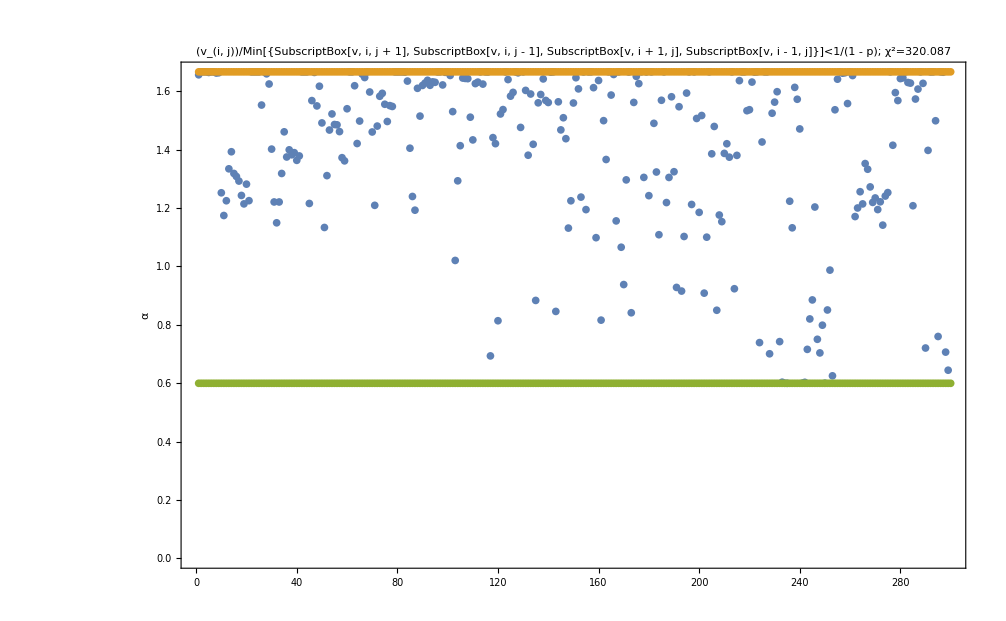

1

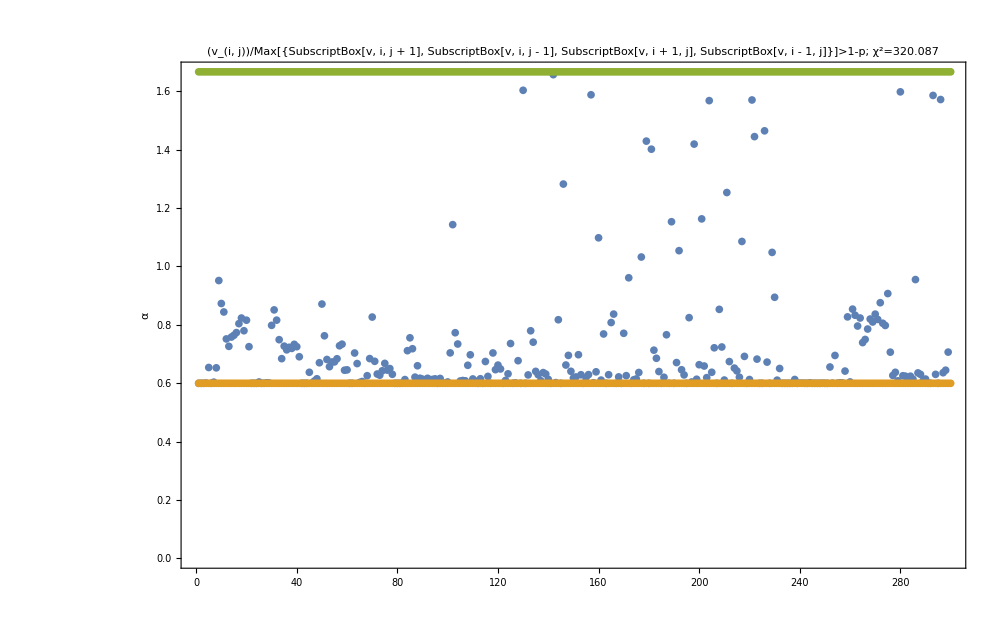

1

```mathematica
tmp2=Import [path<>"/results/chi2Values/chi2cov_324.442_maxIter_100_continuous_0.4_InteriorPoint.dat"];
tmp3=Flatten[tmp2/. 1->Nothing];
var=Thread[V1->tmp3];
p=0.4;

Join[
Flatten[Table[Subscript[v, i,j]/Min[{Subscript[v, i,j+1],Subscript[v, i,j-1],Subscript[v, i+1,j],Subscript[v, i-1,j]}],
{i,2,mecDim-1},{j,i+1,mecDim-1}]],


Flatten[Table[Subscript[v, i,j]/Min[{Subscript[v, i,j+1],Subscript[v, i-1,j]}],
{i,2,mecDim-1},{j,i,i}]],


Flatten[Table[Subscript[v, 1,j]/Min[{Subscript[v, 1,j+1],Subscript[v, 1,j-1],Subscript[v, 1+1,j]}],
{j,2,mecDim-1}]],


Flatten[Table[Subscript[v, i,mecDim]/Min[{Subscript[v, i,mecDim-1],Subscript[v, i-1,mecDim],Subscript[v, i+1,mecDim]}],
{i,2,mecDim-1}]],


{Subscript[v, 1,1]/Subscript[v, 1,2],Subscript[v, 24,24]/Subscript[v, 23,24]}]/.var;

ListPlot[
{%,ConstantArray[1/(1-p),300],ConstantArray[1-p,300]},
PlotLabel->"(v_(i, j))/Min[{SubscriptBox[v, i, j + 1], SubscriptBox[v, i, j - 1], SubscriptBox[v, i + 1, j], SubscriptBox[v, i - 1, j]}]<1/(1 - p);  χ^2=320.087",
Frame->True,
FrameLabel->{,α},
PlotRange->All]

Count[Thread[%%≤1/(1-0.4)],False]



Join[
Flatten[Table[Subscript[v, i,j]/Max[{Subscript[v, i,j+1],Subscript[v, i,j-1],Subscript[v, i+1,j],Subscript[v, i-1,j]}],
{i,2,mecDim-1},{j,i+1,mecDim-1}]],


Flatten[Table[Subscript[v, i,j]/Max[{Subscript[v, i,j+1],Subscript[v, i-1,j]}],
{i,2,mecDim-1},{j,i,i}]],


Flatten[Table[Subscript[v, 1,j]/Max[{Subscript[v, 1,j+1],Subscript[v, 1,j-1],Subscript[v, 1+1,j]}],
{j,2,mecDim-1}]],


Flatten[Table[Subscript[v, i,mecDim]/Max[{Subscript[v, i,mecDim-1],Subscript[v, i-1,mecDim],Subscript[v, i+1,mecDim]}],
{i,2,mecDim-1}]],


{Subscript[v, 24,24]/Subscript[v, 23,24],Subscript[v, 1,1]/Subscript[v, 1,2]}
]/.var;

ListPlot[
{%,ConstantArray[1-p,300],ConstantArray[1/(1-p),300]},
PlotLabel->"(v_(i, j))/Max[{SubscriptBox[v, i, j + 1], SubscriptBox[v, i, j - 1], SubscriptBox[v, i + 1, j], SubscriptBox[v, i - 1, j]}]>1-p;  χ^2=320.087",
Frame->True,
FrameLabel->{,α},
PlotRange->All
]

Count[Thread[%%≥0.6],False]
```

```mathematica
tomek=Import[path<>"/results/tomek.dat"];
chi2cov[Flatten@tomek]
```

chi2cov[{0.641003,0.544853,0.463125,0.393656,0.334608,0.284417,0.241754,0.205491,0.174667,0.148467,0.152882,0.179861,0.211601,0.248943,0.292874,0.344557,0.405362,0.476896,0.561054,0.476896,0.561054,0.660064,0.735162,0.754122,0.,0.463125,0.393656,0.334608,0.284417,0.241754,0.205491,0.174667,0.148467,0.142815,0.150566,0.152882,0.179861,0.211601,0.248943,0.292874,0.344557,0.405362,0.476896,0.561054,0.660064,0.735162,0.864897,0.887202,0.,0.,0.334608,0.284417,0.241754,0.205491,0.174667,0.148467,0.142815,0.168017,0.177136,0.168017,0.18495,0.212606,0.246777,0.290326,0.341559,0.401835,0.472747,0.556173,0.654321,0.769789,0.887202,1.04377,0.,0.,0.,0.241754,0.205491,0.174667,0.148467,0.142815,0.168017,0.197667,0.208395,0.197667,0.217588,0.250125,0.290326,0.341559,0.401835,0.472747,0.556173,0.654321,0.769789,0.905634,1.04377,1.22796,0.,0.,0.,0.,0.174667,0.148467,0.142815,0.168017,0.197667,0.23255,0.245171,0.23255,0.255986,0.294265,0.255529,0.294542,0.34652,0.407671,0.479613,0.56425,0.663824,0.780969,0.918788,1.08093,0.,0.,0.,0.,0.,0.142815,0.168017,0.197667,0.23255,0.273588,0.288436,0.273588,0.30116,0.346194,0.300622,0.34652,0.407671,0.479613,0.56425,0.663824,0.780969,0.918788,1.08093,1.27168,0.,0.,0.,0.,0.,0.,0.197667,0.23255,0.273588,0.321868,0.339337,0.321868,0.354306,0.407287,0.353673,0.407671,0.479613,0.56425,0.663824,0.780969,0.918788,1.08093,1.27168,1.49609,0.,0.,0.,0.,0.,0.,0.,0.273588,0.321868,0.378669,0.39922,0.354306,0.41683,0.479161,0.416086,0.377529,0.444152,0.522532,0.614743,0.723227,0.850856,1.00101,1.1338,1.33389,0.,0.,0.,0.,0.,0.,0.,0.,0.339337,0.39922,0.46967,0.41683,0.490389,0.563718,0.489513,0.427613,0.503074,0.591852,0.696297,0.819173,0.963733,1.1338,1.33389,1.56928,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.353673,0.416086,0.489513,0.563718,0.663198,0.575897,0.489513,0.511379,0.601622,0.707791,0.832695,0.979642,1.15252,1.35591,1.59518,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.353673,0.416086,0.489513,0.575897,0.677526,0.575897,0.489513,0.511379,0.601622,0.707791,0.832695,0.979642,1.15252,1.35591,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.353673,0.416086,0.489513,0.575897,0.527205,0.448124,0.434672,0.511379,0.601622,0.707791,0.832695,0.979642,1.15252,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.353673,0.416086,0.489513,0.448124,0.527205,0.448124,0.434672,0.511379,0.601622,0.707791,0.832695,0.979642,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.353673,0.416086,0.380905,0.448124,0.437889,0.372205,0.434672,0.511379,0.601622,0.707791,0.832695,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.353673,0.323769,0.380905,0.448124,0.434672,0.369471,0.434672,0.511379,0.601622,0.707791,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.275204,0.323769,0.380905,0.446194,0.379265,0.369471,0.434672,0.511379,0.601622,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.275204,0.323769,0.379265,0.440889,0.374756,0.369471,0.434672,0.511379,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.275204,0.322375,0.374756,0.434212,0.369081,0.369471,0.434672,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.274019,0.318542,0.369081,0.433293,0.368299,0.369471,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.270761,0.313718,0.368299,0.433293,0.368299,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.266661,0.313054,0.368299,0.433293,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.334608,0.393656,0.463125,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.463125,0.544853,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.641003}]

```mathematica
q=Flatten[Transpose@nonmecVanillaMatrix];
w=Flatten[Partition[mecDist.Flatten[ConstantArray[1,24^2]],12]];
Thread[{q,w}]
```

{{5.23×10^-41,3.97567×10^-41},{5.08268×10^-41,4.61815×10^-41},{6.62958×10^-41,4.98064×10^-41},{5.8193×10^-41,4.44132×10^-41},{4.6407×10^-41,3.11217×10^-41},{3.02014×10^-41,1.79185×10^-41},{1.62056×10^-41,1.14643×10^-41},{6.62958×10^-42,6.04161×10^-42},{4.05141×10^-42,3.90494×10^-42},{1.84155×10^-42,2.41664×10^-42},{1.62056×10^-42,1.25548×10^-42},{8.10282×10^-43,5.21641×10^-43},{2.1141×10^-40,1.32355×10^-40},{2.29825×10^-40,1.58408×10^-40},{2.77706×10^-40,1.69253×10^-40},{2.79179×10^-40,1.40725×10^-40},{1.85628×10^-40,9.79625×10^-41},{1.28172×10^-40,6.18307×10^-41},{6.48225×10^-41,3.32436×10^-41},{3.94092×10^-41,1.91416×10^-41},{1.80472×10^-41,1.19506×10^-41},{1.43641×10^-41,8.02355×10^-42},{7.80817×10^-42,4.06409×10^-42},{2.57817×10^-42,1.76533×10^-42},{4.70148×10^-40,2.52289×10^-40},{6.32572×10^-40,2.98308×10^-40},{6.85609×10^-40,3.13891×10^-40},{6.613×10^-40,2.66347×10^-40},{4.90036×10^-40,1.75568×10^-40},{3.06066×10^-40,1.01035×10^-40},{1.68502×10^-40,5.85962×10^-41},{8.42509×10^-41,3.61391×10^-41},{5.15173×10^-41,2.16503×10^-41},{2.78995×10^-41,1.37262×10^-41},{1.6132×10^-41,7.52843×10^-42},{7.07155×10^-42,3.13869×10^-42},{8.57425×10^-40,3.7178×10^-40},{1.06957×10^-39,4.29514×10^-40},{1.18448×10^-39,4.40507×10^-40},{1.12924×10^-39,3.6954×10^-40},{8.4564×10^-40,2.43462×10^-40},{5.07531×10^-40,1.38485×10^-40},{2.46768×10^-40,8.07513×10^-41},{1.46219×10^-40,4.89812×10^-41},{8.04757×10^-41,2.97954×10^-41},{4.82486×10^-41,1.8589×10^-41},{2.90965×10^-41,1.00703×10^-41},{1.1123×10^-41,4.32343×10^-42},{1.21542×10^-39,4.398×10^-40},{1.4423×10^-39,5.06464×10^-40},{1.65224×10^-39,5.15659×10^-40},{1.4121×10^-39,4.23767×10^-40},{1.07841×10^-39,2.74377×10^-40},{6.14341×10^-40,1.52779×10^-40},{3.17483×10^-40,9.09483×10^-41},{1.8968×10^-40,5.5126×10^-41},{1.07546×10^-40,3.36488×10^-41},{5.98504×10^-41,2.15214×10^-41},{3.56524×10^-41,1.18917×10^-41},{1.34801×10^-41,4.85686×10^-42},{1.40105×10^-39,4.69389×10^-40},{1.7178×10^-39,5.4121×10^-40},{1.8003×10^-39,5.44924×10^-40},{1.68244×10^-39,4.40124×10^-40},{1.14913×10^-39,2.78268×10^-40},{6.8653×10^-40,1.54135×10^-40},{3.88199×10^-40,9.32765×10^-41},{2.22827×10^-40,5.79258×10^-41},{1.25962×10^-40,3.49308×10^-41},{7.49511×10^-41,2.33928×10^-41},{3.39582×10^-41,1.26667×10^-41},{1.65003×10^-41,5.03664×10^-42},{1.58521×10^-39,4.62345×10^-40},{1.79735×10^-39,5.39×10^-40},{1.89901×10^-39,5.30984×10^-40},{1.68023×10^-39,4.14808×10^-40},{1.17565×10^-39,2.60379×10^-40},{7.05682×10^-40,1.50009×10^-40},{3.77886×10^-40,8.78538×10^-41},{2.25774×10^-40,5.66585×10^-41},{1.27251×10^-40,3.55276×10^-41},{7.88183×10^-41,2.34739×10^-41},{4.40499×10^-41,1.23544×10^-41},{1.56163×10^-41,4.88928×10^-42},{9.4803×10^-40,2.1878×10^-40},{1.81761×10^-39,4.18404×10^-40},{1.84818×10^-39,4.19022×10^-40},{1.55022×10^-39,3.27367×10^-40},{9.70128×10^-40,2.00331×10^-40},{5.69039×10^-40,1.15999×10^-40},{3.21903×10^-40,6.995×10^-41},{1.87286×10^-40,4.61373×10^-41},{1.15833×10^-40,2.95302×10^-41},{7.09917×10^-41,1.87327×10^-41},{3.89672×10^-41,1.02545×10^-41},{1.64266×10^-41,4.23944×10^-42},{2.72549×10^-41,3.87547×10^-42},{1.04563×10^-39,1.54297×10^-40},{1.39037×10^-39,2.02541×10^-40},{1.07178×10^-39,1.61002×10^-40},{6.52277×10^-40,1.0147×10^-40},{3.81201×10^-40,5.88246×10^-41},{2.52661×10^-40,3.74874×10^-41},{1.53585×10^-40,2.63105×10^-41},{8.96835×10^-41,1.72038×10^-41},{5.8193×10^-41,1.09265×10^-41},{3.23008×10^-41,6.16244×10^-42},{1.23752×10^-41,2.71136×10^-42},{0,0.},{7.40303×10^-41,4.89223×10^-42},{7.26307×10^-40,4.18492×10^-41},{6.01082×10^-40,4.09945×10^-41},{3.4658×10^-40,2.70988×10^-41},{2.14356×10^-40,1.7167×10^-41},{1.36275×10^-40,1.11843×10^-41},{9.94437×10^-41,7.9204×10^-42},{6.64799×10^-41,5.20905×10^-42},{3.94092×10^-41,3.79074×10^-42},{2.21723×10^-41,2.33412×10^-42},{8.50796×10^-42,9.5929×10^-43},{0,0.},{0,0.},{3.75676×10^-41,5.92372×10^-43},{1.66623×10^-40,2.1573×10^-42},{1.27288×10^-40,1.45883×10^-42},{9.92227×10^-41,9.99076×10^-43},{6.67378×10^-41,7.16152×10^-43},{5.07163×10^-41,5.39324×10^-43},{3.41423×10^-41,4.35438×10^-43},{2.3093×10^-41,2.93976×10^-43},{1.22868×10^-41,1.80364×10^-43},{5.12687×10^-42,1.00792×10^-43},{0,0.},{0,0.},{0,0.},{4.41972×10^-43,0.},{1.41431×10^-41,0.},{3.24849×10^-41,0.},{2.85072×10^-41,0.},{2.3314×10^-41,0.},{1.53585×10^-41,0.},{9.83387×10^-42,0.},{6.87266×10^-42,0.},{2.69603×10^-42,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{7.18204×10^-43,0.},{1.76789×10^-42,0.},{2.87282×10^-42,0.},{2.83138×10^-42,0.},{2.76232×10^-42,0.},{1.49166×10^-42,0.},{7.78975×10^-43,0.}}

{{75,5.23×10^-41},{75,2.1141×10^-40},{100,4.70148×10^-40},{75,8.57425×10^-40},{75,1.21542×10^-39},{75,1.40105×10^-39},{75,1.58521×10^-39},{150,9.4803×10^-40},{150,2.72549×10^-41},{150,0},{250,0},{250,0},{1000,0}}

{{75,3.97567×10^-41},{75,1.32355×10^-40},{100,2.52289×10^-40},{75,3.7178×10^-40},{75,4.398×10^-40},{75,4.69389×10^-40},{75,4.62345×10^-40},{150,2.1878×10^-40},{150,3.87547×10^-42},{150,0.},{250,0.},{250,0.},{1000,0.}}

{{{75,5.23×10^-41},{75,3.97567×10^-41}},{{75,2.1141×10^-40},{75,1.32355×10^-40}},{{100,4.70148×10^-40},{100,2.52289×10^-40}},{{75,8.57425×10^-40},{75,3.7178×10^-40}},{{75,1.21542×10^-39},{75,4.398×10^-40}},{{75,1.40105×10^-39},{75,4.69389×10^-40}},{{75,1.58521×10^-39},{75,4.62345×10^-40}},{{150,9.4803×10^-40},{150,2.1878×10^-40}},{{150,2.72549×10^-41},{150,3.87547×10^-42}},{{150,0},{150,0.}},{{250,0},{250,0.}},{{250,0},{250,0.}},{{1000,0},{1000,0.}}}